# Práctica III

Definiciones:

```mathematica
sz={{1,0},{0,-1}};sp={{0,1},{0,0}};sm=Transpose[sp];sx=(sp+sm);sy=(sp-sm)/(I);s1[1]=sx;s1[2]=sy;s1[3]=sz;s1[4]={{1,0},{0,1}};s1[i_,j_]=KroneckerProduct[s1[i],s1[j]];
fs=FullSimplify;
mf=MatrixForm;
prod=KroneckerProduct;
id=IdentityMatrix;
s={sx,sy,sz};
daga=ConjugateTranspose;

(* Transpuesta parcial General *)
Clear[nu,nn,au,i,j];
ind[nu_,nn_]:={iaux=1+Floor[(nu-1)/nn],nu-(iaux-1)*nn};
rhotp[au_]:=(nn=Sqrt[Length[au]];
Table[{i,j}=ind[it,nn];{k,l}=ind[jt,nn];
au[[nn*(i-1)+l,nn*(k-1)+j]],{it,nn^2},{jt,nn^2}]); 

(* Base Estándar *)

st0={1,0};st1={0,1};
st00=Flatten[prod[st0,st0]];
st01=Flatten[prod[st0,st1]];
st10=Flatten[prod[st1,st0]];
st11=Flatten[prod[st1,st1]];

(* Proyectores en la Base Estándar *)

P0={{1,0},{0,0}};
P1={{0,0},{0,1}};

n[1]={1,0,0}; n[2]={0,1,0};n[3]={0,0,1};n[4]={1,0,1}/Sqrt[2];
σ={s1[1],s1[2],s1[3]};

(* Rotación General de un qubit *)

R[i_,θ_]=MatrixExp[-I θ n[i].σ/2] ;
```

## I. Compuertas Lógicas Cuánticas

```mathematica
1)a)X ⊗ I
```

```mathematica
XI=MatrixForm[s1[1,4]]
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

```mathematica
b)I ⊗ X
```

```mathematica
IX=s1[4,1]
```

```mathematica
{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}}
```

```mathematica
IXinv=Transpose[IX]
```

{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
IX.IXinv
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
c)X ⊗ X
```

```mathematica
XX=s1[1,1]
```

{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}

```mathematica
MatrixForm[XX]
```

(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
XXinv=Transpose[XX]
```

{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}

```mathematica
XX.XXinv
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
c)Ux=P0⊗ I+P1⊗ X
```

```mathematica
P0={{1,0},{0,0}}
```

{{1,0},{0,0}}

```mathematica
MatrixForm[P0]
```

(1 | 0
0 | 0)

```mathematica
P1={{0,0},{0,1}}
```

{{0,0},{0,1}}

```mathematica
MatrixForm[P1]
```

(0 | 0
0 | 1)

```mathematica
Ux=KroneckerProduct[P0,s1[4]]+KroneckerProduct[P1,s1[1]]
```

{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
-I MatrixExp[I Ux Pi/2]
```

{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
MatrixForm[Ux]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
Ux.Transpose[Ux]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
(*Se trata del Control Not porque al 00 y 01 lo deja igual pero al 10 y 11 cambia el segundo*)
e1={1,0,0,0};e2={0,1,0,0};e3={0,0,1,0};e4={0,0,0,1};

Ux.e1
```

{1,0,0,0}

```mathematica
Ux.e2
```

{0,1,0,0}

```mathematica
Ux.e3
```

{0,0,0,1}

```mathematica
Ux.e4
```

{0,0,1,0}

```mathematica
e[1]=e1;e[2]=e2;e[3]=e3;e[4]=e4;
```

```mathematica
2) W=Ux(H⊗ I) transforma base computacional en base de Bell , con H=(X+Z)/Sqrt[2]
```

```mathematica
H=(s1[1]+s1[3])/Sqrt[2]
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

```mathematica
W=Ux.KroneckerProduct[H,s1[4]]
```

{{1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)},{0,1/(√2),0,-1/(√2)},{1/(√2),0,-1/(√2),0}}

```mathematica
MatrixForm[W]
```

(1/(√2) | 0 | 1/(√2) | 0
0 | 1/(√2) | 0 | 1/(√2)
0 | 1/(√2) | 0 | -1/(√2)
1/(√2) | 0 | -1/(√2) | 0)

```mathematica
Bell[i_]=W.e[i]
```

{{1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)},{0,1/(√2),0,-1/(√2)},{1/(√2),0,-1/(√2),0}}.e[i]

```mathematica
Bell[1]
```

{1/(√2),0,0,1/(√2)}

```mathematica
Bell[2]
```

{0,1/(√2),1/(√2),0}

```mathematica
Bell[3]
```

{1/(√2),0,0,-1/(√2)}

```mathematica
Bell[4]
```

{0,1/(√2),-1/(√2),0}

```mathematica
Wtr=Transpose[W]
```

{{1/(√2),0,0,1/(√2)},{0,1/(√2),1/(√2),0},{1/(√2),0,0,-1/(√2)},{0,1/(√2),-1/(√2),0}}

```mathematica
Wtr.Bell[1]
```

{1,0,0,0}

```mathematica
Gra=-Graphics-
```

```mathematica
3)Swap Us=Ux.Uxbar.Ux
```

```mathematica
Uxbar=KroneckerProduct[s1[4],P0]+KroneckerProduct[s1[1],P1]
```

{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}

```mathematica
MatrixForm[Uxbar]
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

```mathematica
Us=Ux.Uxbar.Ux
```

{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}

```mathematica
Us.e1
```

{1,0,0,0}

```mathematica
Us.e2
```

{0,0,1,0}

```mathematica
Us.e3
```

{0,1,0,0}

```mathematica
Us.e4
```

{0,0,0,1}

# Rotaciones

```mathematica
En 2D, rotacion horaria
```

```mathematica
R2={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}
```

{{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}

```mathematica
Cos[θ]*s1[4]+ I Sin[θ]*s1[2]
```

{{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}

```mathematica
Manipulate[Graphics[{Hue[θ/40],Arrow[{{0,0},{Cos[2θ Pi/40],-Sin[2θ Pi /40]}}]}, PlotRange->{{-1,1},{-1,1},{-1,1}},Axes->True],{θ,1,40}]
```

```mathematica
Rotación horaria alrededor del eje z
```

```mathematica
Rz={{Cos[θ],Sin[θ],0},{-Sin[θ],Cos[θ],0},{0,0,1}}
```

{{Cos[θ],Sin[θ],0},{-Sin[θ],Cos[θ],0},{0,0,1}}

```mathematica
Rz.{1,0,0}
{Cos[θ],Sin[θ],0}
```

```mathematica
Ejes=Show[Graphics3D@{Style [Text[X,{1.55,0,0}],Bold,15]},Graphics3D@{Style [Text[Y,{0,1.55,0}],Bold,15]},Graphics3D@{Style [Text[Z,{0,0,1.55}],Bold,15]},Boxed->False];
-Graphics3D-

flechas=Show[Graphics3D@{Arrow[{{0,0,0},{1.44,0,0}}]},Graphics3D@{Arrow[{{0,0,0},{0,1.44,0}}]},Graphics3D@{Arrow[{{0,0,0},{0,0,1.44}}]},Boxed->False];
-Graphics3D-

esfera=SphericalPlot3D[1,{θ,0,Pi},{ϕ,0,2Pi},Boxed->False,Axes->False,Mesh->10,MeshStyle->{Cyan,Directive[Cyan]},PlotStyle->{LightGray,Opacity[0.16]}];
-Graphics3D-
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
R
```

```mathematica
Manipulate[Show[Ejes,flechas,esfera,Graphics3D[{Hue[θ/40],Arrow[{{0,0,0},{Cos[2θ Pi/40],-Sin[2θ Pi /40],0}}]}, PlotRange->{{-1,1},{-1,1},{-1,1}},Axes->True]],{θ,1,40}]
```

Show::gcomb: Could not combine the graphics objects in Show[Ejes,flechas,esfera,].

```mathematica
1)Rotación de ángulo θ alrededor de eje n
```

```mathematica
a)
```

```mathematica
n[1]={1,0,0}; n[2]={0,1,0};n[3]={0,0,1};n[4]={1,0,1}/Sqrt[2];
σ={s1[1],s1[2],s1[3]};

R[i_,θ_]=MatrixExp[-I θ n[i].σ/2]
```

MatrixExp[-1/2 ⅈ θ n[i].{{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}}}]

```mathematica
Clear[i]
```

```mathematica
R[i_,θ_]=MatrixExp[-I θ n[i].σ/2]
```

MatrixExp[-1/2 ⅈ θ 201[i].{{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}}}]

```mathematica
R[3,ϕ].R[2,θ].R[3,α].R[2,-θ].R[3,-ϕ]//FullSimplify
```

{{Cos[α/2]-ⅈ Cos[θ] Sin[α/2],Sin[α/2] Sin[θ] (-ⅈ Cos[ϕ]-Sin[ϕ])},{Sin[α/2] Sin[θ] (-ⅈ Cos[ϕ]+Sin[ϕ]),Cos[α/2]+ⅈ Cos[θ] Sin[α/2]}}

```mathematica
nn={Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

```mathematica
(* Como satisface *)
```

```mathematica
(nn.σ).(nn.σ) //FullSimplify
```

{{1,0},{0,1}}

```mathematica
(* Se ve que la rotación general también se la puede escribir así*)
```

```mathematica
Cos[α/2]s1[4]+ I*Sin[α/2](nn.σ)
```

{{Cos[α/2]+ⅈ Cos[θ] Sin[α/2],ⅈ Sin[α/2] (Cos[ϕ] Sin[θ]-ⅈ Sin[θ] Sin[ϕ])},{ⅈ Sin[α/2] (Cos[ϕ] Sin[θ]+ⅈ Sin[θ] Sin[ϕ]),Cos[α/2]-ⅈ Cos[θ] Sin[α/2]}}

```mathematica
(*Recorre toda la superficie de la esfera de bloch para estados puros ρ=|ϕxϕ|; |r|=1 *)
```

```mathematica
Manipulate[Show[Ejes,flechas,esfera,Graphics3D[{Hue[θ/40],Arrow[{{0,0,0},{Sin[θ Pi /40]Cos[2ϕ Pi/40],Sin[θ Pi /40]Sin[2ϕ Pi/40],Cos[θ Pi /40]}}]}, PlotRange->{{-1,1},{-1,1},{-1,1}},Axes->True]],{θ,1,40},{ϕ,1,40}]
```

Show::gcomb: Could not combine the graphics objects in Show[Ejes,flechas,esfera,].

```mathematica
(*Para estados de 1-qubit generales ρ=1/2(I+r.σ) con|r|⩽1 *)
```

```mathematica
Manipulate[Show[Ejes,flechas,esfera,Graphics3D[{Hue[θ/40],Arrow[{{0,0,0},r{Sin[θ Pi /40]Cos[2ϕ Pi/40],Sin[θ Pi /40]Sin[2ϕ Pi/40],Cos[θ Pi /40]}}]}, PlotRange->{{-1,1},{-1,1},{-1,1}},Axes->True]],{θ,0,40},{ϕ,0,40},{r,0,1}]
```

Show::gcomb: Could not combine the graphics objects in Show[Ejes,flechas,esfera,].

```mathematica
Manipulate[Show[Ejes,flechas,esfera,Graphics3D[{Hue[10],Arrow[{{0,0,0},n[4]}]}, PlotRange->{{-1,1},{-1,1},{-1,1}},Axes->True],
Graphics3D[{Hue[m+1/40],Arrow[{{0,0,0},(Rn4^m).{1,0,0}}]}, PlotRange->{{-1,1},{-1,1},{-1,1}},Axes->True]],{m,1,10,1}]
```

```mathematica
R[4,π].s1[1].Transpose[R[4,π]]
```

{{-1,0},{0,1}}

```mathematica
-1 s1[3]
```

{{-1,0},{0,1}}

```mathematica
R[4,π].s1[2].Transpose[R[4,π]]
```

{{0,-ⅈ},{ⅈ,0}}

```mathematica
s1[2]
```

{{0,-ⅈ},{ⅈ,0}}

```mathematica
R[4,π].s1[3].Transpose[R[4,π]]
```

{{0,-1},{-1,0}}

```mathematica
-1 s1[1]+
```

{{0,-1},{-1,0}}

```mathematica
Es
```

```mathematica
-1 s1[1]+ s1[2]-1 s1[3]
```

```mathematica
Rn4={{-1,0,0},{0,1,0},{0,0,-1}}
```

{{-1,0,0},{0,1,0},{0,0,-1}}

```mathematica
(Rn4^4).{1,0,0}
```

{1,0,0}

```mathematica
b)
```

```mathematica
X=I R[1,π]
```

{{0,1},{1,0}}

```mathematica
Y=I R[2,π]
```

{{0,-ⅈ},{ⅈ,0}}

```mathematica
Z=I R[3,π]
```

{{1,0},{0,-1}}

```mathematica
H=I R[4,π] // FullSimplify
```

ⅈ MatrixExp[-1/2 ⅈ π 201[4].{{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}}}]

```mathematica
X.Z.X
```

{{-1,0},{0,1}}

```mathematica
X.Y.X
```

{{0,ⅈ},{-ⅈ,0}}

```mathematica
H.X.H
```

{{1,0},{0,-1}}

```mathematica
H.Z.H;
```

```mathematica
rhoa=(3/4) prod[st0,st0]+(1/4) prod[st1,st1]
```

{{3/4,0},{0,1/4}}

```mathematica
sta=√(3/4)st0 + √(1/4)st1;  stb=√(3/4)st0 - √(1/4)st1;
```

```mathematica
(* Los estados sta,stb no ortogonales *)
```

```mathematica
sta.stb
```

1/2

```mathematica
a sta + b stb
```

{(√3 a)/2+(√3 b)/2,a/2-b/2}

```mathematica
rhoab=(1/2) prod[sta,sta]+(1/2) prod[stb,stb]
```

{{3/4,0},{0,1/4}}

```mathematica
Eigenvalues[prod[stb,stb]]
```

{1,0}

```mathematica
prod[sta,sta]+ prod[stb,stb]
```

{{3/2,0},{0,1/2}}

```mathematica
a prod[sta,sta]+b prod[stb,stb]//fs
```

{{(3 (a+b))/4,1/4 √3 (a-b)},{1/4 √3 (a-b),(a+b)/4}}

```mathematica
Solve[(√3 a)/2+(√3 b)/2==0&&a/2-b/2==0,{a,b}]
```

{{a→0,b→0}}

```mathematica
Solve[a+b==4&&a+b==1/3,{a,b}]
```

{}

```mathematica
{(3 (4))/4,1/4 √3 (a-b)},{1/4 √3 (a-b),(a+b)/4}
```

```mathematica
x1 prod[sta,sta]+x2 prod[stb,stb]
```

{{(3 x1)/4+(3 x2)/4,(√3 x1)/4-(√3 x2)/4},{(√3 x1)/4-(√3 x2)/4,x1/4+x2/4}}

```mathematica
^
```

```mathematica
sta
```

{(√3)/2,1/2}

```mathematica
(* Gráfico de los estados sta y stb en en eje X,Z *)
```

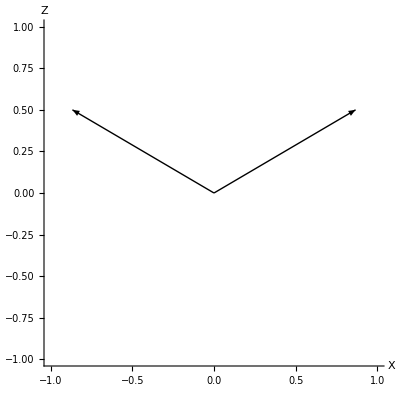

```mathematica
Graphics[{Arrow[{{0,0},{√(3/4),1/2}}],Arrow[{{0,0},{-√(3/4),1/2}}]} ,FrameLabel->{"x","C[x]"},
FrameStyle->Directive[Black,16],PlotRange->{{-1,1},{-1,1},{-1,1}},Axes->True,AxesLabel->{X,Z}]
```

```mathematica
Transpose[{sta,stb}]
```

```mathematica
(* Evidentemente no se puede general un conjunto de medida a partir de los proyectores en sta y stb *)
```

```mathematica
Sovle[{prod[sta,sta]+ prod[stb,stb]}.{x1,x2}==s1[4],{x1,x2}]
```

Sovle[False,{x1,x2}]

```mathematica
(* Para encontrar el que falta notamos que un qubit (I + r.σ)/2 por lo que para que ∑M^†M=I, |r|=0 *)
```

```mathematica
ArcCos[sta.st0]
```

π/6

```mathematica
ArcCos[Tr[prod[sta,sta].s1[3]]]
```

π/3

```mathematica
Sin[Pi/3]
```

(√3)/2

```mathematica
Tr[prod[sta,sta].s1[1]]
```

(√3)/2

```mathematica
ArcCos[1]
```

0

```mathematica
(s1[4]+(√3)/2 s1[1]+1/2 s1[3])/2
```

{{3/4,(√3)/4},{(√3)/4,1/4}}

```mathematica
ArcCos[Tr[prod[stb,stb].s1[3]]]
```

π/3

```mathematica
Tr[prod[stb,stb].s1[1]]
```

-(√3)/2

```mathematica
ArcCos[-1]
```

π

```mathematica
(s1[4]-(√3)/2 s1[1]+1/2 s1[3])/2
```

{{3/4,-(√3)/4},{-(√3)/4,1/4}}

```mathematica
(s1[4]-1 s1[3])/2
```

{{0,0},{0,1}}

```mathematica
(* El estado que falta para completar la medida es st1 *)
```

```mathematica
prod[st1,st1]
```

{{0,0},{0,1}}

```mathematica
(* Gráfico de los estados sta,stb y st1 en en eje X,Z *)
```

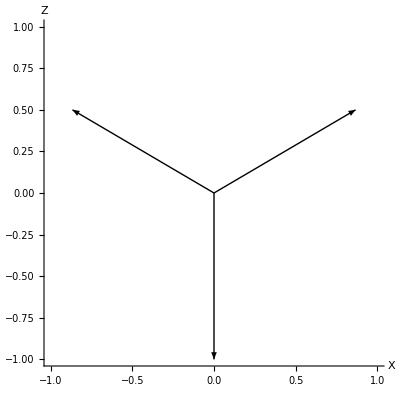

```mathematica
Graphics[{Arrow[{{0,0},{√(3/4),1/2}}],Arrow[{{0,0},{-√(3/4),1/2}}],Arrow[{{0,0},{0,-1}}]} ,FrameLabel->{"x","C[x]"},
FrameStyle->Directive[Black,16],PlotRange->{{-1,1},{-1,1},{-1,1}},Axes->True,AxesLabel->{X,Z}]
```

```mathematica
(prod[sta,sta]+prod[stb,stb]+(s1[4]-1 s1[3])/2)(2/3)
```

{{1,0},{0,1}}

```mathematica
Tr[rhoa.P0]
```

3/4

```mathematica
(* Conjunto de operadores de medida de los estados no-ortogonales *)
```

```mathematica
Pa= (2/3)prod[sta,sta];Pb= (2/3)prod[stb,stb];Pc= (2/3)prod[st1,st1];
```

```mathematica
(* Suma de probabilidades en la base no-ortogonal *)

Tr[Pa.rhoab]+Tr[Pb.rhoab]+Tr[Pc.rhoab]
```

1

```mathematica
Tr[Pa.rhoab]
```

5/12

```mathematica
(* Suma de probabilidades en la base estándar *)
```

```mathematica
Tr[P0.rhoa]+Tr[P1.rhoa]
```

1

```mathematica
rhoa
```

{{3/4,0},{0,1/4}}

```mathematica
Tr[P1.rhoa]
```

1/4

```mathematica
Tr[Pa.rhoab]
```

5/12

```mathematica
rhoalbe=({{q, 0}, {0, 1-q}})
```

{{q,0},{0,1-q}}

```mathematica
(* Estado st0 y st1 en la base al be *)
```

```mathematica
a0 st0 +b0 st1; a1 st0 +b1 st1;
```

```mathematica
p prod[a0 st0 +b0 st1,a0 st0 +b0 st1]+(1-p) prod[a1 st0 +b1 st1,a1 st0 +b1 st1]
```

{{a1^2 (1-p)+a0^2 p,a1 b1 (1-p)+a0 b0 p},{a1 b1 (1-p)+a0 b0 p,b1^2 (1-p)+b0^2 p}}

```mathematica
U2={{a0^2,a1^2},{b0^2,b1^2}}//mf
```

(a0^2 | a1^2
b0^2 | b1^2)

```mathematica
1-q={{b0^2 p +(1-p), b1^2}}
```

Set::write: Tag Plus in 1-q is Protected.

{{1-(3 p)/4,3/4}}

```mathematica
p/4 +(1-p)/4//fs
```

1/4

```mathematica
b0=√(1/4);b1=-√(1/4);
```

```mathematica
x1=1/4
```

1/4

```mathematica
sta.sta
```

1

```mathematica
Inverse[{sta,stb}]
```

{{1/(√3),1/(√3)},{1,-1}}

```mathematica
Usta={Normalize[{1/(√3),1/(√3)}],Normalize[{1,-1}]}
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

```mathematica
Transpose[{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}].{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}
```

{{1,0},{0,1}}

```mathematica
Usta.sta//fs
```

{(√(2+√3))/2,(√(2-√3))/2}

```mathematica
Usta.st0
```

{1/(√2),1/(√2)}

```mathematica
Usta.st1
```

{1/(√2),-1/(√2)}

```mathematica
prod[{1/(√2),1/(√2)},{1/(√2),1/(√2)}]
```

{{1/2,1/2},{1/2,1/2}}

```mathematica
(* Se ve que q⩽p para todo p ∈ (1/2,1)
```

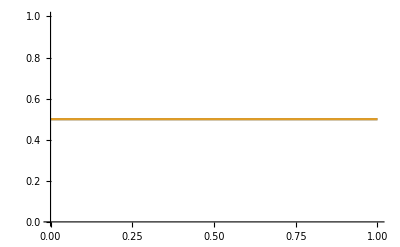
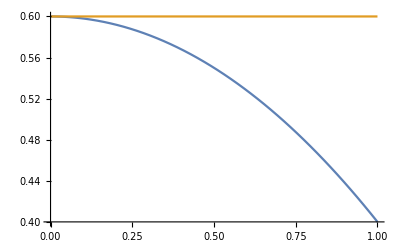
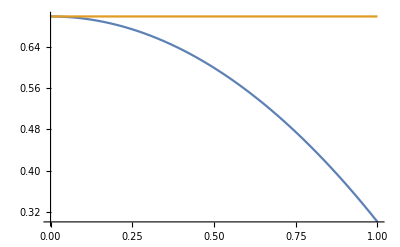
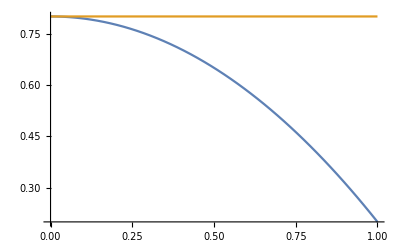
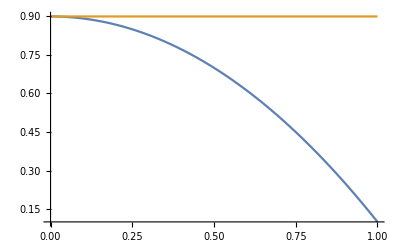
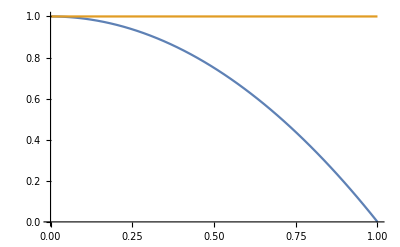

```mathematica
Table[Plot[{p+x^2(1-2p),p},{x,0,1}],{p,1/2,1,.1}]
```

```mathematica
U2{p,1-p}
```

{p (a0^2 | a1^2
b0^2 | b1^2),(1-p) (a0^2 | a1^2
b0^2 | b1^2)}

```mathematica
prod[st1,st1]
```

{{0,0},{0,1}}

```mathematica
stm=(st0-st1)/√2
```

{1/(√2),-1/(√2)}

```mathematica
M1dagM1=p({{0, 0}, {0, 1}});
```

```mathematica
Tr[M1dagM1.s1[4]]
```

p

```mathematica
M1dagM1
```

{{0,0},{0,p}}

```mathematica
(r1.SIGM)/2
```

{{0,0},{0,p}}

```mathematica
M2dagM2=p prod[stm,stm]
```

{{p/2,-p/2},{-p/2,p/2}}

```mathematica
σ
```

{{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}}}

```mathematica
SIGM={{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}},{{1,0},{0,1}}}
```

{{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}},{{1,0},{0,1}}}

```mathematica
{{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}},{{1,0},{0,1}}
```

```mathematica
(r2.SIGM)/2
```

{{p/2,-p/2},{-p/2,p/2}}

```mathematica
r1=Table[Tr[M1dagM1.s1[i]],{i,1,4}]
```

{0,0,-p,p}

```mathematica
r2=Table[Tr[M2dagM2.s1[i]],{i,1,4}]
```

{-p,0,0,p}

```mathematica
Tr[M2dagM2.s1[1]]
```

-p

```mathematica
{0,0,-p}+{-p,0,0}
```

{-p,0,-p}

```mathematica
r3={p,0,p,2-2p}
```

{p,0,p,2-2 p}

```mathematica
{p,0,p,q}
```

{p,0,p,q}

```mathematica
(r1.SIGM+r2.SIGM+r3.SIGM)/2
```

{{1,0},{0,1}}

```mathematica
r3.SIGM/2
```

{{(2-p)/2,p/2},{p/2,1/2 (2-3 p)}}

```mathematica
M3dagM3=(s1[4]+{p,0,p}.σ)/2
```

{{(1+p)/2,p/2},{p/2,(1-p)/2}}

```mathematica
p
```

```mathematica
Eigensystem[r3.SIGM/2]
```

{{1/2 (2-2 p-√2 p),1/2 (2-2 p+√2 p)},{{1-√2,1},{1+√2,1}}}

```mathematica
Sqrt[{1/2 (2-2 p-√2 p),1/2 (2-2 p+√2 p)}]
```

{(√(2-2 p-√2 p))/(√2),(√(2-2 p+√2 p))/(√2)}

```mathematica
Diag=({{(√(2-2 p-√2 p))/(√2), 0}, {0, (√(2-2 p-√2 p))/(√2)}})
```

{{(√(2-2 p-√2 p))/(√2),0},{0,(√(2-2 p-√2 p))/(√2)}}

```mathematica
Ss={{1-√2,1},{1+√2,1}}
```

{{1-√2,1},{1+√2,1}}

```mathematica
M1dagM1+M2dagM2+M3dagM3//FullSimplify
```

{{1/2+p,0},{0,1/2+p}}

```mathematica
Clear[p]
```

```mathematica
p=1;
```

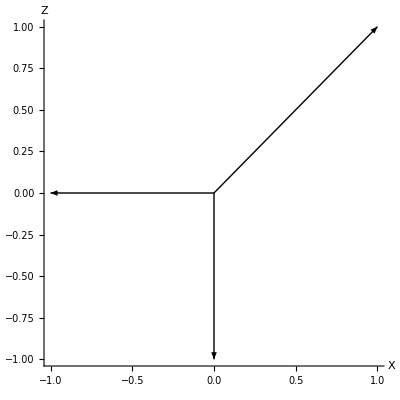

```mathematica
Graphics[{Arrow[{{0,0},{0,-p}}],Arrow[{{0,0},{-p,0}}],Arrow[{{0,0},{p,p}}]} ,FrameLabel->{"x","C[x]"},
FrameStyle->Directive[Black,16],PlotRange->{{-1,1},{-1,1},{-1,1}},Axes->True,AxesLabel->{X,Z}]
```

```mathematica
Tr[q{{(1+p)/2,p/2},{p/2,(1-p)/2}}]//fs
```

q

```mathematica
Tr[M1dagM1+M2dagM2+(2-2p){{(1+p)/2,p/2},{p/2,(1-p)/2}}]//fs
```

2

```mathematica
M1dagM1+M2dagM2+(2-2p){{(1+p)/2,p/2},{p/2,(1-p)/2}}//fs
```

{{1/2 (2+p-2 p^2),1/2 (1-2 p) p},{1/2 (1-2 p) p,1-p/2+p^2}}

```mathematica
P0={{1,0},{0,0}};
P1={{0,0},{0,1}};

Ux=KroneckerProduct[P0,s1[4]]+KroneckerProduct[P1,s1[1]]
{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}
```

```mathematica
{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}//mf
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
Uz=KroneckerProduct[P0,s1[4]]+KroneckerProduct[P1,s1[3]]

Z=({{1, 0}, {0, -1}})
```

```mathematica
00-} 00
01-} 01
```

```mathematica
10-} 1Z 0 -} 10 
11-} 1Z 1 -} - 11
```

```mathematica
{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}}//mf
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
(* Ux=(I⊗H) Uz (I⊗H) *)
```

```mathematica
Hz=λ (KroneckerProduct[s1[3],s1[4]]+KroneckerProduct[s1[4],s1[3]]-KroneckerProduct[s1[3],s1[3]])
```

{{λ,0,0,0},{0,λ,0,0},{0,0,λ,0},{0,0,0,-3 λ}}

```mathematica
^
```

{{ⅇ^(-ⅈ λ τ),0,0,0},{0,ⅇ^(-ⅈ λ τ),0,0},{0,0,ⅇ^(-ⅈ λ τ),0},{0,0,0,ⅇ^(3 ⅈ λ τ)}}

```mathematica
si
```

```mathematica
λ *τ= (Pi/4) + 2 k Pi
```

Set::write: Tag Times in λ τ is Protected.

π/4+2 k π

```mathematica
Exp[-I (π/4)]//FullSimplify
```

-(-1)^(3/4)

```mathematica
Sin[ (π/4)]
```

1/(√2)

```mathematica
N[ⅇ^(-ⅈ (π/4))]
```

0.707107-0.707107 ⅈ

```mathematica
(*Hay una fase afuera*)
```

```mathematica
I ⅇ^(-(ⅈ π)/4)*MatrixExp[- I  (Pi/4)(KroneckerProduct[s1[3],s1[4]]+KroneckerProduct[s1[4],s1[3]]-KroneckerProduct[s1[3],s1[3]])]
```

```mathematica
Uz=I ⅇ^(-(ⅈ π)/4)*MatrixExp[- I  (Pi/4)(KroneckerProduct[s1[3],s1[4]]+KroneckerProduct[s1[4],s1[3]]-KroneckerProduct[s1[3],s1[3]])];
```

```mathematica
{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}}//mf
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
(* Como vimos HZH=X rota al segundo qubit Ux=(I⊗H)Uz(I⊗H) *)
```

```mathematica
I ⅇ^(-(ⅈ π)/4)*MatrixExp[- I  (Pi/4)(KroneckerProduct[s1[3],s1[4]]+KroneckerProduct[s1[4],s1[1]]-KroneckerProduct[s1[3],s1[1]])]//FullSimplify
```

{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
H
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

```mathematica
prod[s1[4],H]
```

{{1/(√2),1/(√2),0,0},{1/(√2),-1/(√2),0,0},{0,0,1/(√2),1/(√2)},{0,0,1/(√2),-1/(√2)}}

```mathematica
prod[s1[4],H].Uz.prod[s1[4],H]
```

{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
II.1) A partir de la forma general de un estado de dos qubits
Subscript[ρ, AB]=[I⊗I+∑_(i,j) Subscript[δ, ij] (Subscript[r, i]^A Subscript[σ, i]⊗I+Subscript[r, i]^B I⊗Subscript[σ, i] )+Subscript[J, ij]  Subscript[σ, i] ⊗Subscript[σ, j] ]/4
```

```mathematica
II.1)
e)Expresar en la forma anterior el estado puro Subscript[ρ, AB]= |ψ><ψ|,para
	
       i)|ψ>=(|00>+|11>) /√2

        ii)|ψ>=(|01>-|10>) /√2.
```

```mathematica
(* i)|ψ>=(|00>+|11>) /√2 *)
```

```mathematica
stpsi1=(st00+st11)/√2
```

{1/(√2),0,0,1/(√2)}

```mathematica
rhopsi1=prod[stpsi1,stpsi1]
```

{{1/2,0,0,1/2},{0,0,0,0},{0,0,0,0},{1/2,0,0,1/2}}

```mathematica
(* Subscript[r, i]^A=Tr(Subscript[σ, i]⊗I ρ)=0;Subscript[r, i]^B= Tr(I⊗Subscript[σ, i] ρ)=0 *)
```

```mathematica
Tr[s1[4,3].rhopsi1]
```

0

```mathematica
(*Subscript[r, i]^A=Tr(Subscript[σ, i]⊗I ρ)=0 *)
```

```mathematica
Table[Tr[s1[4,i].rhopsi1],{i,1,3}]
```

{0,0,0}

```mathematica
(* Subscript[J, ij] =Tr(Subscript[σ, i]⊗Subscript[σ, j] ρ) *)
```

```mathematica
Jij=Table[Tr[s1[i,j].rhopsi1],{i,1,3},{j,1,3}]
```

{{1,0,0},{0,-1,0},{0,0,1}}

```mathematica
Tr[s1[1,3].rhopsi1]
```

0

```mathematica
(s1[4,4]+ Sum[Tr[s1[i,j].rhopsi1] s1[i,j] ,{i,1,3},{j,1,3}])/4
```

{{1/2,0,0,1/2},{0,0,0,0},{0,0,0,0},{1/2,0,0,1/2}}

```mathematica
Jj={{1,0,0},{0,-1,0},{0,0,1}}
```

{{1,0,0},{0,-1,0},{0,0,1}}

```mathematica
Jj[[1,1]]
```

1

```mathematica
(s1[4,4]+ Sum[Jj[[i,j]] s1[i,j] ,{i,1,3},{j,1,3}])/4
```

{{1/2,0,0,1/2},{0,0,0,0},{0,0,0,0},{1/2,0,0,1/2}}

```mathematica
(* i)|ψ>=(|01>-|10>) /√2 *)
```

```mathematica
stpsi2=(st01+-st10)/√2;

rhopsi2=prod[stpsi2,stpsi2]
```

{{0,0,0,0},{0,1/2,-1/2,0},{0,-1/2,1/2,0},{0,0,0,0}}

```mathematica
(* Subscript[r, i]^A=Tr(Subscript[σ, i]⊗I ρ)=0;Subscript[r, i]^B= Tr(I⊗Subscript[σ, i] ρ)=0 *)
```

```mathematica
Tr[s1[4,3].rhopsi2]
```

0

```mathematica
Jij2=Table[Tr[s1[i,j].rhopsi2],{i,1,3},{j,1,3}]
```

{{-1,0,0},{0,-1,0},{0,0,-1}}

```mathematica
(s1[4,4]+ Sum[Tr[s1[i,j].rhopsi2] s1[i,j] ,{i,1,3},{j,1,3}])/4
```

{{0,0,0,0},{0,1/2,-1/2,0},{0,-1/2,1/2,0},{0,0,0,0}}

```mathematica
II.Estados no puros de dos qubits y traspuesta parcial
```

```mathematica
2)Para el estado|ψ>=(|01>-|10>) /√2  considerar el estado Subscript[ρ, AB]=x|ψ><ψ|+(1-x) I⊗I/4
```

```mathematica
a)Indicar para qué valores de x es Subscript[ρ, AB] un estado físico.
```

```mathematica
ψ=1/√2. ({{0}, {1}, {-1}, {0}} );
```

```mathematica
ψ.Transpose[ψ];
```

```mathematica
rho[x_]=x ψ.Transpose[ψ]+(1-x) s1[4,4]/4 //Chop
```

{{(1-x)/4,0,0,0},{0,(1-x)/4+0.5 x,-0.5 x,0},{0,-0.5 x,(1-x)/4+0.5 x,0},{0,0,0,(1-x)/4}}

```mathematica
MatrixForm[rho[x]]
```

((1-x)/4 | 0 | 0 | 0
0 | (1-x)/4+0.5 x | -0.5 x | 0
0 | -0.5 x | (1-x)/4+0.5 x | 0
0 | 0 | 0 | (1-x)/4)

```mathematica
(* Para ver que es un estado físico tiene que cumplir Tr[Subscript[ρ, AB]]=1, ser hermítica y semidefinida positiva. Las dos primeras condiciones se ven directamente *)
```

```mathematica
Tr[rho[x]]//Chop
```

1

```mathematica
(* x es real *)
```

```mathematica
Transpose[rho[x]]
```

{{(1-x)/4,0,0,0},{0,(1-x)/4+0.5 x,-0.5 x,0},{0,-0.5 x,(1-x)/4+0.5 x,0},{0,0,0,(1-x)/4}}

```mathematica
(* Para ver que es semidefinida positiva, los autovalores tienen que ser mayor o iguales a cero *)
```

```mathematica
Eigenvalues[rho[x]]
```

{(1-x)/4,(1-x)/4,0.5 (0.5-0.5 x),0.5 (0.5+1.5 x)}

```mathematica
Reduce[{(1-x)/4>0,0.5 (0.5-0.5 x)>0,0.5 (0.5+1.5 x)>0},x]
```

-0.333333<x<1.

```mathematica
(* Para ser un estado físico x ∈ [-1/3,1] *)
```

{1,1,-b,b}

```mathematica
b) Indicar para qué valores de x es Subscript[ρ, AB] un estado puro. 
Como vimos un estado puro cumple  Subscript[ρ, AB] ^2= Subscript[ρ, AB]
```

```mathematica
Solve[rho[x].rho[x]==rho[x],x]
```

{{x→1.}}

```mathematica
(* Es evidente de la expresión que para x=1 se recupera el estado puro |ψ><ψ| *=)
```

```mathematica
ψ.Transpose[ψ]
```

{{0.,0.,0.,0.},{0.,0.5,-0.5,0.},{0.,-0.5,0.5,0.},{0.,0.,0.,0.}}

```mathematica
rho[1]
```

{{0.,0.,0.,0.},{0.,0.5,-0.5,0.},{0.,-0.5,0.5,0.},{0.,0.,0.,0.}}

```mathematica
rho[1].rho[1]
```

{{0.,0.,0.,0.},{0.,0.5,-0.5,0.},{0.,-0.5,0.5,0.},{0.,0.,0.,0.}}

```mathematica
MatrixForm[ψ.Transpose[ψ]]
```

(0. | 0. | 0. | 0.
0. | 0.5 | -0.5 | 0.
0. | -0.5 | 0.5 | 0.
0. | 0. | 0. | 0.)

```mathematica
c) Indicar para qué valores de x se viola la desigualdad de Bell|Subscript[Trρ, AB] O|≤2,con O el
observable CHSH descripto en clase.
```

```mathematica
(*R2 es la rotación θ alrededor del eje y para generar los operadores rotados (los primados) del observable O=X⊗X'+Z⊗Z'+X⊗Z'-Z⊗X' O=X⊗(X'+Z')+Z⊗(Z'-X') *)
```

```mathematica
R2=R[2,θ]
```

{{Cos[θ/2],-Sin[θ/2]},{Sin[θ/2],Cos[θ/2]}}

```mathematica
R2.{1,0}
```

{Cos[θ/2],Sin[θ/2]}

```mathematica
R2T=Transpose[R[2,θ]]
```

{{Cos[θ/2],Sin[θ/2]},{-Sin[θ/2],Cos[θ/2]}}

```mathematica
.b4
```

```mathematica
(-sz+sx)/Sqrt[2]
```

{{-1/(√2),1/(√2)},{1/(√2),1/(√2)}}

```mathematica
R2.sx.R2T//fs
```

{{-Sin[θ],Cos[θ]},{Cos[θ],Sin[θ]}}

```mathematica
psi=Flatten[ψ]
```

{0.,0.707107,-0.707107,0.}

```mathematica
Tr[rho[x].prod[sx,R2.sx.R2T]]//fs
```

-1. x Cos[θ]

```mathematica
Tr[rho[x].prod[sz,R2.sz.R2T]]//fs
```

-1. x Cos[θ]

```mathematica
Tr[rho[x].prod[sz,R2.sz.R2T]]//fs
```

-1. x Cos[θ]

```mathematica
Tr[rho[x].prod[sx,R2.sz.R2T]]//fs
```

-1. x Sin[θ]

```mathematica
Psi=Flatten[ψ]
```

{0.,0.707107,-0.707107,0.}

```mathematica
prod[sx,R2.sz.R2T]//fs
```

{{0,0,Cos[θ],Sin[θ]},{0,0,Sin[θ],-Cos[θ]},{Cos[θ],Sin[θ],0,0},{Sin[θ],-Cos[θ],0,0}}

```mathematica
R2.sz.R2T//fs
```

{{Cos[θ],Sin[θ]},{Sin[θ],-Cos[θ]}}

```mathematica
Tr[rho[x].prod[sz,R2.sx.R2T]]//fs
```

1. x Sin[θ]

```mathematica
(* En general O *)
```

```mathematica
Ob=prod[sx,R2.sx.R2T]+prod[sz,R2.sz.R2T]+prod[sx,R2.sz.R2T]-prod[sz,R2.sx.R2T];
```

```mathematica
Tr[(s1[4,4]/4).Ob]//fs
```

0

```mathematica
Tr[rho[x].Ob]//fs
```

-2. x Cos[θ]-2. x Sin[θ]

```mathematica
-2 x (Cos[θ]+ Sin[θ])
```

```mathematica
Obmedio=-2 √2 x Cos[θ-π/4]
```

-2 √2 x Cos[π/4-θ]

```mathematica
(* Clásicamente Valormedio(Ob)=+-1 (+-1 - +-1) + +-1 (+-1 + +-1) 2 *).b4`
```

```mathematica
Un estado clásico
```

```mathematica
prod[st00,st00]
```

{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
rhocl=(prod[st00,st00]+prod[st11,st11])/2
```

{{1/2,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1/2}}

```mathematica
stp=(st0+st1)/√2;stm=(st0-st1)/√2;
```

```mathematica
stpp=Flatten[prod[stp,stp]];stmm=Flatten[prod[stm,stm]];
```

```mathematica
st0p=Flatten[prod[st0,stp]];
```

```mathematica
st1m=Flatten[prod[st1,stm]];
```

```mathematica
stpth=(R2.st0+R2.st1)/√2
```

{(Cos[θ/2]-Sin[θ/2])/(√2),(Cos[θ/2]+Sin[θ/2])/(√2)}

```mathematica
st0pth=Flatten[prod[st0,stpth]];

stpth
```

{(Cos[θ/2]-Sin[θ/2])/(√2),(Cos[θ/2]+Sin[θ/2])/(√2)}

```mathematica
θ=.;N[R2.sx.R2T+R2.sz.R2T]
```

{{Cos[0.5 θ]^2-2. Cos[0.5 θ] Sin[0.5 θ]-1. Sin[0.5 θ]^2,Cos[0.5 θ]^2+2. Cos[0.5 θ] Sin[0.5 θ]-1. Sin[0.5 θ]^2},{Cos[0.5 θ]^2+2. Cos[0.5 θ] Sin[0.5 θ]-1. Sin[0.5 θ]^2,-1. Cos[0.5 θ]^2+2. Cos[0.5 θ] Sin[0.5 θ]+Sin[0.5 θ]^2}}

```mathematica
st0.R2.sx.R2T.st0//fs
```

-Sin[θ]

```mathematica
st1.R2.sx.R2T.st1//fs
```

Sin[θ]

```mathematica
qubit=(s1[4]+r1.sig)/2
```

```mathematica
r1th={r1z Cos[θ]+r1x Sin[θ],r1y,r1x Cos[θ]-r1z Sin[θ]}/2
```

{1/2 (r1z Cos[θ]+r1x Sin[θ]),r1y/2,1/2 (r1x Cos[θ]-r1z Sin[θ])}

```mathematica
qubitth=(s1[4]+r1th.sig)/2
```

{{1/2 (1+1/2 (r1x Cos[θ]-r1z Sin[θ])),1/2 (-(ⅈ r1y)/2+1/2 (r1z Cos[θ]+r1x Sin[θ]))},{1/2 ((ⅈ r1y)/2+1/2 (r1z Cos[θ]+r1x Sin[θ])),1/2 (1+1/2 (-r1x Cos[θ]+r1z Sin[θ]))}}

```mathematica
{{(1+r1z)/2,1/2 (r1x-ⅈ r1y)},{1/2 (r1x+ⅈ r1y),(1-r1z)/2}}
```

```mathematica
Tr[qubitth.R2.sz.R2T]//fs
```

r1x/2

```mathematica
Tr[qubit.R2.sx.R2T]//fs
```

r1x Cos[θ]-r1z Sin[θ]

```mathematica
Tr[qubit.R2.sy.R2T]//fs
```

r1y

```mathematica
r1x
```

r1x

```mathematica
R2.st0
```

{Cos[θ/2],Sin[θ/2]}

```mathematica
R2.st1
```

{-Sin[θ/2],Cos[θ/2]}

```mathematica
r1
```

{r1x,r1y,r1z}

```mathematica
r1th={r1x,r1y,r1z}
```

```mathematica
Pp=prod[stp,stp]
```

{{1/2,1/2},{1/2,1/2}}

```mathematica
Tr[qubit.R2.sz.R2T]//fs
```

r1z Cos[θ]+r1x Sin[θ]

```mathematica
Tr[qubitth.(R2.sx.R2T+R2.sz.R2T)]//fs
```

(r1x+r1z)/2

```mathematica
r1th.r1th//fs
```

1/4 (r1x^2+r1y^2+r1z^2)

```mathematica
Tr[qubitth]//fs
```

1

```mathematica
rhocl2=(prod[st00,st00]+prod[stpp,stpp]+prod[stmm,stmm]+prod[st11,st11])/4
```

{{3/8,0,0,1/8},{0,1/8,1/8,0},{0,1/8,1/8,0},{1/8,0,0,3/8}}

```mathematica
Tr[rhocl4]
```

1

```mathematica
rhocl3=(prod[st0p,st0p]+prod[st1m,st1m])/2
```

{{1/4,1/4,0,0},{1/4,1/4,0,0},{0,0,1/4,-1/4},{0,0,-1/4,1/4}}

```mathematica
rhocl4=prod[st0p,st0p]
```

{{1/2,1/2,0,0},{1/2,1/2,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
st0.s1[3].st0
```

1

```mathematica
stp.s1[3].stp
```

```mathematica
stp.H.stp
```

```mathematica
rhocl5=prod[st0pth,st0pth]
```

{{1/2 (Cos[θ/2]-Sin[θ/2])^2,1/2 (Cos[θ/2]-Sin[θ/2]) (Cos[θ/2]+Sin[θ/2]),0,0},{1/2 (Cos[θ/2]-Sin[θ/2]) (Cos[θ/2]+Sin[θ/2]),1/2 (Cos[θ/2]+Sin[θ/2])^2,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Clear[θ];stpth=(R2.st0+R2.st1)/√2
stmth=(R2.st0-R2.st1)/√2
```

{(Cos[θ/2]-Sin[θ/2])/(√2),(Cos[θ/2]+Sin[θ/2])/(√2)}

{(Cos[θ/2]+Sin[θ/2])/(√2),(-Cos[θ/2]+Sin[θ/2])/(√2)}

```mathematica
st0pth=Flatten[prod[st0,stpth]];
```

```mathematica
st0mth=Flatten[prod[st0,stmth]];
```

```mathematica
rhocl6=prod[st0mth,st0mth]
```

{{1/2 (Cos[π/8]+Sin[π/8])^2,1/2 (-Cos[π/8]+Sin[π/8]) (Cos[π/8]+Sin[π/8]),0,0},{1/2 (-Cos[π/8]+Sin[π/8]) (Cos[π/8]+Sin[π/8]),1/2 (-Cos[π/8]+Sin[π/8])^2,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Tr[rhocl6]//fs
```

1

```mathematica
P0
```

```mathematica
prod[P0,qubitth]
```

```mathematica
{{1/2 (1+1/2 (r1x Cos[θ]-r1z Sin[θ])),1/2 (-(ⅈ r1y)/2+1/2 (r1z Cos[θ]+r1x Sin[θ])),0,0},{1/2 ((ⅈ r1y)/2+1/2 (r1z Cos[θ]+r1x Sin[θ])),1/2 (1+1/2 (-r1x Cos[θ]+r1z Sin[θ])),0,0},
{0,0,0,0},{0,0,0,0}}
```

```mathematica
Clear[θ]
```

```mathematica
stp.sx.stp
```

1

```mathematica
Tr[Pp.sx]
```

1

```mathematica
θ=Pi/2;Tr[(R2.sx.R2T+R2.sz.R2T)qubitth]//fs
```

r1z/2

```mathematica
Tr[(prod[sx,R2.sx.R2T]+prod[sx,R2.sz.R2T])prod[Pp,qubitth]]
```

0

```mathematica
θ=.;N[Tr[Ob prod[Pp,qubitth]]]//fs
```

0.

1.

```mathematica
Cos[-π/4] Cos[θ] - Sin[θ]Sin[-π/4]//fs
```

(Cos[θ]+Sin[θ])/(√2)

```mathematica
El valor máx lo toma para θ=Pi/4
```

```mathematica
Reduce[2 √2 x >2,x]
```

x>1/(√2)

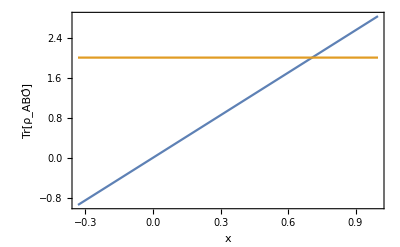

```mathematica
Plot[{2 √2 x,2},{x,-1/3,1},Frame->True,
FrameLabel->{"x","Tr[ρ_ABÔ]"},
FrameStyle->Directive[Black,16]]
```

```mathematica
(* Para x=1 en función de θ *)
```

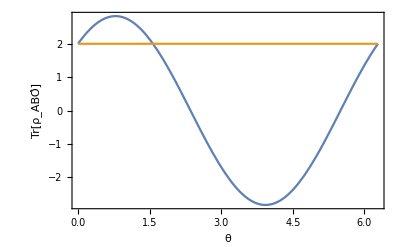

```mathematica
Plot[{2 √2 Cos[θ-π/4],2},{θ,0,2 Pi},Frame->True,
FrameLabel->{"θ","Tr[ρ_ABÔ]"},
GridLines->{{Pi/4},{}},
FrameStyle->Directive[Black,16]]
```

```mathematica
r1={r1x,r1y,r1z};
```

```mathematica
sig={s1[1],s1[2],s1[3]};
```

```mathematica
q1=(s1[4]+r1.sig)/2;
```

```mathematica
Tr[s1[1].q1]
```

1/2 (r1x-ⅈ r1y)+1/2 (r1x+ⅈ r1y)

### d) Indicar para qué valores de x es ρ_AB entrelazado

## Transpuesta parcial en B 10 01 -> 11 00, 01 10→00 11

```mathematica
(1-x)/4+0.5 x//FullSimplify
```

0.25+0.25 x

```mathematica
Para 1-qubit el criterio es necesario y suficiente λ(ρ^tb)<0  -> Entrelazamiento
```

```mathematica
rhotb[x_]=({{(1-x)/4, 0, 0, -0.5 x}, {0, (1-x)/4+0.5 x, 0, 0}, {0, 0, (1-x)/4+0.5 x, 0}, {-0.5 x, 0, 0, (1-x)/4}})
```

{{(1-x)/4,0,0,-0.5 x},{0,(1-x)/4+0.5 x,0,0},{0,0,(1-x)/4+0.5 x,0},{-0.5 x,0,0,(1-x)/4}}

```mathematica
(* Teniendo en cuenta que para ser un estado físico -1/3<x<1 *)
```

```mathematica
Eigenvalues[rhotb[x]]
```

{0.5 (0.5-1.5 x),0.5 (0.5+0.5 x),0.25 (1.+1. x),0.25 (1.+1. x)}

```mathematica
Reduce[0.5(0.5-1.5 x)<0,x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x>0.333333

```mathematica
Reduce[0.5 (0.5+0.5 x)<0,x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x<-1.

```mathematica
Reduce[0.25 (1.+1. x)<0,x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x<-1.

```mathematica
(* Vimos que para ser un estado físico x ∈ [-1/3,1] por lo que para ser entrelazado x ∈ [1/3,1] *)
```

```mathematica
Se puede ver analíticamente
```

```mathematica
Eigenvalues[{{(1-x)/4,0,0,-x/2},{0,(1+x)/4,0,0},{0,0,(1+x)/4,0},{-x/2,0,0,(1-x)/4}}]
```

{1/4 (1-3 x),(1+x)/4,(1+x)/4,(1+x)/4}

```mathematica
Solve[1/4 (1-3 x)==0,x]
```

{{x→1/3}}

```mathematica
prod[s1[2],s1[2]]
```

{{0,0,0,-1},{0,0,1,0},{0,1,0,0},{-1,0,0,0}}

```mathematica
rho[x]
```

{{(1-x)/4,0,0,0},{0,(1-x)/4+0.5 x,-0.5 x,0},{0,-0.5 x,(1-x)/4+0.5 x,0},{0,0,0,(1-x)/4}}

```mathematica
rhotilde= prod[s1[2],s1[2]].rho[x].prod[s1[2],s1[2]]//FullSimplify//Chop
```

{{0.25-x/4,0,0,0},{0,0.25+0.25 x,-0.5 x,0},{0,-0.5 x,0.25+0.25 x,0},{0,0,0,0.25-x/4}}

```mathematica
(1-x)/4+0.4999999999999999 x//FullSimplify
```

0.25+0.25 x

```mathematica
(* rhotilde=rho *)
```

```mathematica
rho[x]//FullSimplify//Chop
```

{{(1-x)/4,0,0,0},{0,0.25+0.25 x,-0.5 x,0},{0,-0.5 x,0.25+0.25 x,0},{0,0,0,(1-x)/4}}

```mathematica
rhotilde. rho[x]
```

{{0.+1/4 (0.+(1-x)/4) (1-x),0.,0.,0.},{0.,0.+((1-x)/4+0.5 x) (0.+(1-x)/4+0.5 x)+0.25 x^2,0.-0.5 ((1-x)/4+0.5 x) x-0.5 (0.+(1-x)/4+0.5 x) x,0.},{0.,0.-0.5 ((1-x)/4+0.5 x) x-0.5 (0.+(1-x)/4+0.5 x) x,0.+((1-x)/4+0.5 x) (0.+(1-x)/4+0.5 x)+0.25 x^2,0.},{0.,0.,0.,0.+1/4 (0.+(1-x)/4) (1-x)}}

```mathematica
Eigenvalues[rhotilde. rho[x]]//FullSimplify
```

{1/16 (-1+x)^2,1/16 (-1+x)^2,0.0625+(-0.125+0.0625 x) x,0.0625+(0.375+0.5625 x) x}

```mathematica
√(Eigenvalues[rhotilde. rho[x]])//FullSimplify
```

{1/4 √((-1+x)^2),1/4 √((-1+x)^2),0.707107 √(0.125+(-0.25+0.125 x) x),0.707107 √(0.125+x (0.75+1.125 x))}

```mathematica
rhotilde2={{0.25-x/4,0,0,0},{0,0.25+0.25 x,-0.5 x,0},{0,-0.5 x,0.25+0.25 x,0},{0,0,0,0.25-x/4}}
```

{{0.25-x/4,0,0,0},{0,0.25+0.25 x,-0.5 x,0},{0,-0.5 x,0.25+0.25 x,0},{0,0,0,0.25-x/4}}

```mathematica
rhotilde2.rhotilde2
```

{{(0.25-x/4)^2,0.,0.,0},{0.,(0.25+0.25 x)^2+0.25 x^2,-1. (0.25+0.25 x) x,0.},{0.,-1. (0.25+0.25 x) x,(0.25+0.25 x)^2+0.25 x^2,0.},{0,0.,0.,(0.25-x/4)^2}}

```mathematica
Eigenvalues[{{(0.25-x/4)^2,0.,0.,0},{0.,(0.25+0.25 x)^2+0.25 x^2,-1. (0.25+0.25 x) x,0.},{0.,-1. (0.25+0.25 x) x,(0.25+0.25 x)^2+0.25 x^2,0.},{0,0.,0.,(0.25-x/4)^2}}]
```

```mathematica
(* Directamente son los autovalores de rho en este caso
```

```mathematica
Eigenvalues[rhotilde2]
```

{0.25 (1.-1. x),0.25 (1.-1. x),0.5 (0.5-0.5 x),0.5 (0.5+1.5 x)}

```mathematica
(* Conc=Max(0, Subscript[λ, 1]-Subscript[λ, 2]-Subscript[λ, 3]-Subscript[λ, 4]) autovalores de R=√√ρ rhotilde √ρ ordenados en forma decreciente *)
```

```mathematica
Conc=0.5 (0.5+1.5 x)-3*(0.25 (1.-1. x))//FullSimplify
```

-0.5+1.5 x

```mathematica
(3x-1)/2
```

## e) Negatividad, Concurrencia y Entrelazamiento de Formación de ρ_AB

```mathematica
(* La Negatividad se calcula sumando los autovalores negativos (cambiados de signo) de ρ^tb
N=∑-Subscript[λ, i]( ρ^tb) en este caso es simplemente -Subscript[λ, 1] *)
```

```mathematica
(* Subscript[λ, 1]=1/4 (1-3 x) *)
```

```mathematica
Neg[x_]=(3x-1)/4;
```

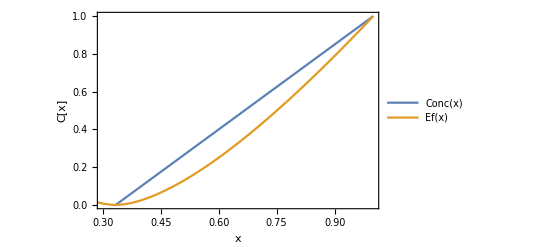

```mathematica
Conc[x_]=(3x-1)/2;
p1=(1+√(1-Conc[x]^2))/2;p2=(1-√(1-Conc[x]^2))/2;
Ef[x_]=-p1 Log2[p1]-p2 Log2[p2];
Plot[{Conc[x],Ef[x]},{x,-1/3,1},Frame->True,FrameLabel->{"x","C[x]"},
FrameStyle->Directive[Black,16],PlotLegends->"Expressions",
GridLines->{{1/3},{}},
GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{.3,1},{0,1}}]
```

```mathematica
(* En el intervalo -1/3≤x≤1/3 C=0 y Ef=-1Log2[1]=0 *)
```

```mathematica
Concu[x_]:=Piecewise[{{0,-1/3≤x≤1/3},{Conc[x],1/3≤x≤1}}]
Eform[x_]:=Piecewise[{{0,-1/3≤x≤1/3},{Ef[x],1/3≤x≤1}}]
```

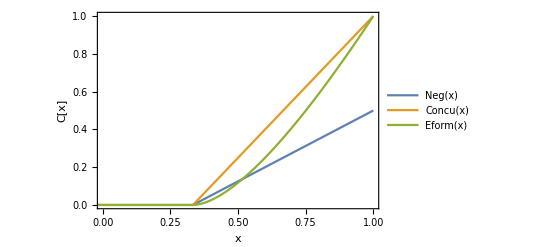

```mathematica
Plot[{Neg[x],Concu[x],Eform[x]},{x,-1/3,1},Frame->True,FrameLabel->{"x","C[x]"},
FrameStyle->Directive[Black,16],PlotLegends->"Expressions",
GridLines->{{1/3},{}},
GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,1},{0,1}}]
```

```mathematica
(* Información Mútua: I(A,B)=S(Subscript[ρ, A])S(Subscript[ρ, B])-S(Subscript[ρ, AB])  *)
```

```mathematica
rho[x]
```

rho[x]

```mathematica
λrho=Eigenvalues[rho[x]]
```

{(1-x)/4,(1-x)/4,0.5 (0.5-0.5 x),0.5 (0.5+1.5 x)}

```mathematica
(* [[]] Selecciona un elemento *)
```

```mathematica
λrho[[1]]
```

(1-x)/4

```mathematica
Map[Tr,Partition[rho[x],{2,2}],{2}]
```

{{0.+(1-x)/2+0.5 x,0.},{0.,0.+(1-x)/2+0.5 x}}

```mathematica
Map[Tr,Partition[rho[x],{2,2}],{2}]
```

{{0.+(1-x)/2+0.5 x,0.},{0.,0.+(1-x)/2+0.5 x}}

```mathematica
(* Esta es otra forma de calcular trazas parciales en la que se reordena y se eligen los índices que se contraen *)
```

```mathematica
rho[x]
```

{{0.+(1-x)/4,0.,0.,0.},{0.,(1-x)/4+0.5 x,-0.5 x,0.},{0.,-0.5 x,(1-x)/4+0.5 x,0.},{0.,0.,0.,0.+(1-x)/4}}

```mathematica
rhop=ArrayReshape[rho[x],{2,2,2,2}]
```

{{{{0.+(1-x)/4,0.},{0.,0.}},{{0.,(1-x)/4+0.5 x},{-0.5 x,0.}}},{{{0.,-0.5 x},{(1-x)/4+0.5 x,0.}},{{0.,0.},{0.,0.+(1-x)/4}}}}

```mathematica
rhoA=TensorContract[ArrayReshape[rhop,{2,2,2,2}],{2,4}]//Chop
rhoB=TensorContract[ArrayReshape[rhop,{2,2,2,2}],{1,3}]
```

{{(1-x)/2+0.5 x,0},{0,(1-x)/2+0.5 x}}

{{0.+(1-x)/2+0.5 x,0.},{0.,0.+(1-x)/2+0.5 x}}

```mathematica
λrhoA=Eigenvalues[rhoA]//Chop
λrhoB=Eigenvalues[rhoB]//Chop
```

{0.5,0.5}

{0.5,0.5}

```mathematica
SrhoA=-Sum[λrhoA[[i]]Log2[λrhoA[[i]]],{i,1,2}]
```

1.

```mathematica
SrhoB=-Sum[λrhoB[[i]]Log2[λrhoB[[i]]],{i,1,2}]
```

1.

```mathematica
SrhoAB[x_]:=-Sum[λrho[[i]]Log2[λrho[[i]]],{i,1,4}]
```

```mathematica
IAB[x_]:=SrhoA+SrhoB-SrhoAB[x]
```

```mathematica
DAB[x_]:=2SrhoB-SrhoAB[x]
```

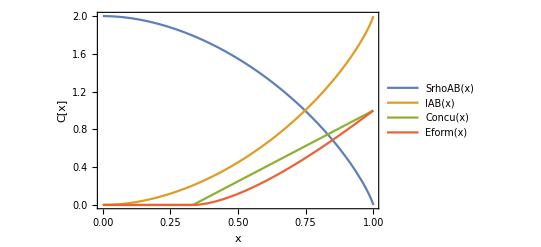

```mathematica
Graf=Plot[{SrhoAB[x],IAB[x],Concu[x],Eform[x]},{x,0,1},Frame->True,FrameLabel->{"x","C[x]"},
FrameStyle->Directive[Black,16],PlotLegends->"Expressions",
GridLines->{{1/3},{}},
GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,1},{0,2}}]
```

```mathematica
...............................
```

```mathematica
Partial Trace
```

```mathematica
A1=({{a1, b1}, {c1, d1}});A2=({{a2, b2}, {c2, d2}});
```

```mathematica
r=KroneckerProduct[A1,A2]
```

{{a1 a2,a1 b2,a2 b1,b1 b2},{a1 c2,a1 d2,b1 c2,b1 d2},{a2 c1,b2 c1,a2 d1,b2 d1},{c1 c2,c1 d2,c2 d1,d1 d2}}

```mathematica
r2={{a,0,0,b},{0,c,d,0},{0,d,e,0},{b,0,0,f}}
```

{{a,0,0,b},{0,c,d,0},{0,d,e,0},{b,0,0,f}}

```mathematica
Map[Tr,Partition[r2,{2,2}],{2}]
```

{{a+c,0},{0,e+f}}

```mathematica
TensorContract[ArrayReshape[r2,{2,2,2,2}],{2,4}]
```

{{a+c,0},{0,e+f}}

```mathematica
TensorContract[ArrayReshape[r2,{2,2,2,2}],{1,3}]
```

{{a+e,0},{0,c+f}}

```mathematica
Map[Tr,Partition[r,{2,2}]]
```

{a1 a2+b1 d2,a2 c1+d1 d2}

```mathematica
Partition[r,{2,2}]//MatrixForm
```

((a1 a2 | a1 b2
a1 c2 | a1 d2) | (a2 b1 | b1 b2
b1 c2 | b1 d2)
(a2 c1 | b2 c1
c1 c2 | c1 d2) | (a2 d1 | b2 d1
c2 d1 | d1 d2))

```mathematica
Map[Tr,Partition[r,{2,2}],{3}]
```

{{{a1 a2+a1 b2,a1 c2+a1 d2},{a2 b1+b1 b2,b1 c2+b1 d2}},{{a2 c1+b2 c1,c1 c2+c1 d2},{a2 d1+b2 d1,c2 d1+d1 d2}}}

```mathematica
rhop=ArrayReshape[rho[x],{2,2,2,2}]
```

{{{{0.+(1-x)/4,0.},{0.,0.}},{{0.,(1-x)/4+0.5 x},{-0.5 x,0.}}},{{{0.,-0.5 x},{(1-x)/4+0.5 x,0.}},{{0.,0.},{0.,0.+(1-x)/4}}}}

```mathematica
rhoA=TensorContract[rhop,{2,4}];rhoA
```

{{0.+(1-x)/2+0.5 x,0.},{0.,0.+(1-x)/2+0.5 x}}

```mathematica
rhoB=TensorContract[rhop,{1,3}];rhoB
```

{{0.+(1-x)/2+0.5 x,0.},{0.,0.+(1-x)/2+0.5 x}}

```mathematica
Directory[]
```

/home/alan